```mathematica
Clear["Global`*"];
```

```mathematica
data=Import["../res/step2/data_000000_000000.dat"];
tdc=data⟦1⟧//First;
data=data⟦2;;⟧;
time=data⟦;;,1⟧;
Print["data number: ",Length@data]
```

data number: 2369

```mathematica
data1=Import["../res/step3/clst_000000_000000.dat"];
time1=data1⟦;;,1⟧;
Print["data number: ",Length@data1]
```

data number: 1392

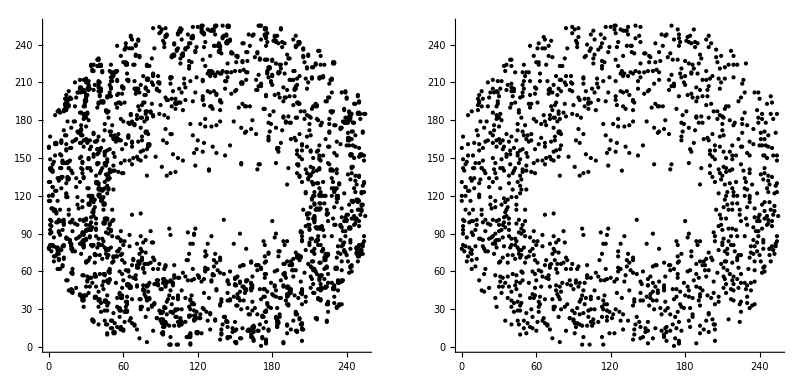

```mathematica
(* 2D scattering *)
GraphicsRow[{
Graphics[Point[data⟦;;,{3,4}⟧,VertexColors->(Hue/@Rescale[time])],Axes->True,GridLines->{Range[250],Range[250]}],
Graphics[Point[data1⟦;;,{3,4}⟧,VertexColors->(Hue/@Rescale[time1])],Axes->True,GridLines->{Range[250],Range[250]}]}]
```

```mathematica
(* 3D scattering *)
GraphicsRow[{
Graphics3D[Point[data⟦;;,{1,3,4}⟧,VertexColors->(Hue/@Rescale[time])],Axes->True,BoxRatios->{1,1,1}],
Graphics3D[Point[data1⟦;;,{1,3,4}⟧,VertexColors->(Hue/@Rescale[time1])],Axes->True,BoxRatios->{1,1,1}]
}]
```

-Graphics-